```mathematica
data=Import["C:\\Users\\Я\\Desktop\\machine-learning-ex2\\ex2\\ex2data1.txt","Data"];
```

```mathematica
data=SortBy[data,Last];
```

```mathematica
Y=data[[;;,3]]/.{0->-1};
X=Table[Flatten@{1,data[[i,{1,2}]]},{i,1,Length[data]}];
```

```mathematica
M[x_,w_,y_]:=w.x*y
L[m_]:=Log[1+Exp[-m]]
dL[m_]:=-ⅇ^-m/(1+ⅇ^-m)
Q[w_]:=Sum[L[M[X[[i]],w,Y[[i]]]],{i,1,Length[X]}]
```

```mathematica
L[m_]:=2(1+Exp[m])^-1
dL[m_]:=-(2 ⅇ^m)/((1+ⅇ^m)^2)
```

```mathematica
Clear[dL]
```

```mathematica
graddecent[Q_,X_,Y_,a_,itermax_]:=Module[{Qt={},i,w1,wt={},m=Length[X],w=Table[RandomReal[{-1,1}],{i,1,Length[X[[1]]]}]},
AppendTo[Qt,Q[w]];
AppendTo[wt,w];
For[i=1,i≤itermax,i++,
w1=w-a/m Sum[dL[M[X[[h]],w,Y[[h]]]]X[[h]]Y[[h]],{h,1,m}];
w=w1;
AppendTo[Qt,Q[w]];
AppendTo[wt,w];
];
{w,wt,Qt}]
```

```mathematica
gradsto[Q_,X_,Y_,a_,itermax_]:=Module[{Qt={},h,w1,wt={},m=Length[X],w=Table[RandomReal[{-1,1}],{i,1,Length[X[[1]]]}]},
AppendTo[Qt,Q[w]];
AppendTo[wt,w];
For[j=1,j≤itermax,j++,
h=RandomInteger[{1,m}];
w1=w-a/m dL[M[X[[h]],w,Y[[h]]]]X[[h]]Y[[h]];
w=w1;
AppendTo[Qt,Q[w]];
AppendTo[wt,w];];
{w,wt,Qt}]
```

```mathematica
gradstoc[Q_,X_,Y_,a_,l_]:=Module[{Qt={},h,w1,wt={},m=Length[X],w=Table[RandomReal[{-1,1}],{i,1,Length[X[[1]]]}]},
AppendTo[Qt,Q[w]];
AppendTo[wt,w];
While[True,
h=RandomInteger[{1,m}];
w1=w-a/m dL[M[X[[h]],w,Y[[h]]]]X[[h]]Y[[h]];
w=w1;
AppendTo[Qt,Q[w]];
AppendTo[wt,w];
If[Abs[Qt[[-1]]-Qt[[-2]]]<l,Break[]];
];
{w,wt,Qt}]
```

```mathematica
Timing[tr=graddecent[Q[#]&,X,Y,10,10000];]
```

{19.3438,Null}

```mathematica
Timing[tr1=gradsto[Q[#]&,X,Y,10,10000];]
```

{7.5625,Null}

```mathematica
Timing[tr2=gradstoc[Q[#]&,X,Y,10,10^-8];]
```

{78.8594,Null}

```mathematica
tr[[1]]
```

{1.71291,20.5562,20.0792}

```mathematica
tr1[[1]]
```

{1.06239,13.5755,12.7063}

```mathematica
tr2[[1]]
```

{1.54276,18.5874,17.8448}

```mathematica
Q[tr[[1]]]
```

20.3498

```mathematica
Q[tr1[[1]]]
```

23.1971

```mathematica
Q[tr2[[1]]]
```

20.4735

```mathematica
trt=NArgMin[Q[{x1,x2,x3}],{x1,x2,x3}]
```

{1.71845,20.6232,20.1472}

```mathematica
Q[trt]
```

20.3498

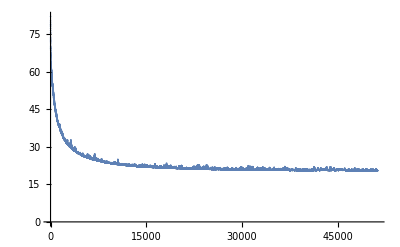

```mathematica
ListPlot[tr2[[3]],PlotRange->Full]
```

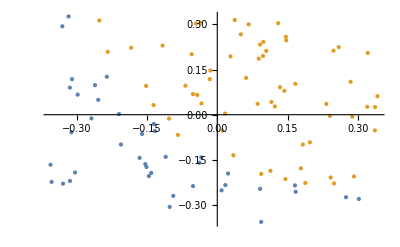

```mathematica
X1=Select[scalled1@data,#[[3]]==0&][[;;,{1,2}]];
X2=Select[scalled1@data,#[[3]]==1&][[;;,{1,2}]];
ListPlot[{X1,X2},PlotStyle->{PointSize[Large]}]
```

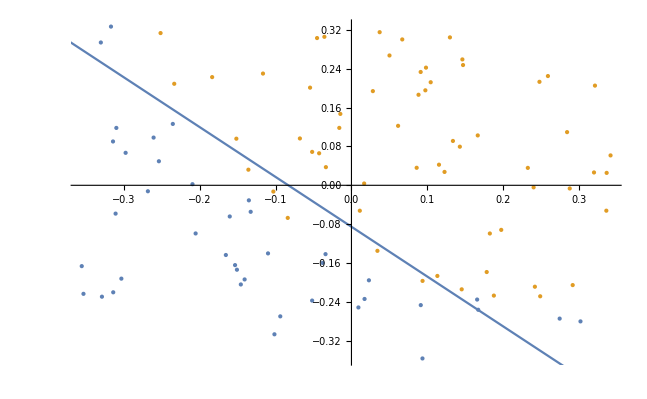

```mathematica
Show[ListPlot[{X1,X2},PlotStyle->{PointSize[Large]}],ContourPlot[tr[[1]].{1,x1,x2}==0,{x1,-1,100},{x2,-1,100}]]
```

```mathematica
X=Table[Flatten@{1,scalled1[data][[i,{1,2}]]},{i,1,Length[data]}];
```

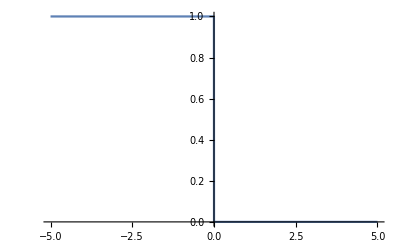

```mathematica
Plot[dL[m],{m,-5,5}]
```